```mathematica
(*Define the functions we'll need throughout the notebook*)
```

```mathematica
G[x_,μ_,σ_,A_]:= A/(√(2π σ^2))E^(-1/2((x-μ)/σ)^2);
H[x_,ω_] := 1/2 ω^2 x^2;
U[x_,ω_,A_,μ_,σ_]:= G[x,μ,σ,A] + H[x,ω];
F [x_,ω_,A_,μ_,σ_]:= -D[U[x,ω,A,μ,σ],{x,1}];
polyfun[N_,x_] := Sum[Subscript[r, n] x^(n-1),{n,1,N+1}];
DampedSine[t_,a_,b_,c_,d_,e_]:= a E^(-b t)Sin[ c t + d]+e;
(* Parameters defined externally because lazy/stupid*)
```

## Realistic parameters

μ=offset of gaussian to trap center
σ=gaussian width
A=amplitude of gaussian
β=damping term
v0=inital velocity

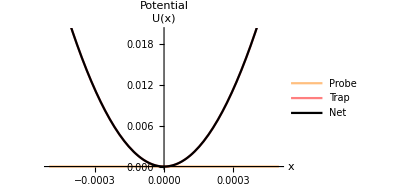
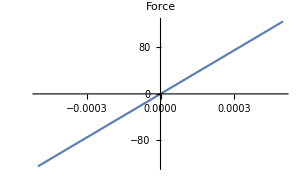
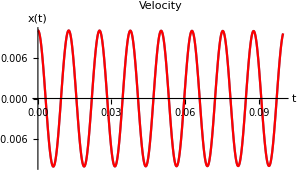
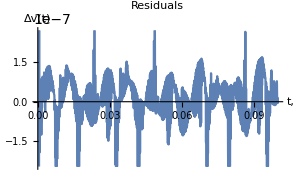
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 1.58404

```mathematica
(*Setting parameters*)
{ω,μ,σ,A,β,v0}={500,10^-5,10^-5,0,0.2,0.01};(* Hz, m, m, au, ?, m/s *)
fsamp=10*ω;
tmax=.1;
dt=1/fsamp;
nsamp=fsamp*tmax;
xrange=0.0005;
sz=300;
(*Doing the work*)
soln=NDSolve[{x''[t] == F [x[t],ω,A,μ,σ]-β x'[t],x[0]==0,x'[0]==v0},x,{t,0,tmax}];
T = Table[n*dt,{n,0,nsamp}];
V =x'[t]/.t->T/.soln[[1]];
Vdata=Table[{T[[i]],V[[i]]},{i,1,Length[T]}];
nlmv = NonlinearModelFit[Vdata,DampedSine[t,a,b,c,d,e] ,{{a,v0},{b,β},{c,ω},{d,π},{e,0}},t];
deltav[t_]:=Evaluate[x'[t]/.soln]-nlmv[t];
(* Generating plots*)
f11 =  Plot[G[x,μ,σ,A] ,{x,-xrange,xrange},PlotStyle->{Orange,Opacity[0.5]},PlotLabel->"Potential",PlotLegends->{"Probe"},AxesLabel->{"x","U(x)"}];
f12=Plot[H[x,ω] ,{x,-xrange,xrange},PlotStyle->{Red,Opacity[0.5]},PlotLegends->{"Trap"}];
f13=Plot[Evaluate[G[x,μ,σ,A] + H[x,ω]], {x,-xrange,xrange},PlotStyle->Black,PlotLegends->{"Net"},AxesLabel->{"x","F(x)"}];
f2=Plot[Evaluate[D[G[x,μ,σ,A] + H[x,ω],{x,1}]], {x,-xrange,xrange},PlotRange->Full,PlotLabel->"Force"];
f41=Plot[Evaluate[x'[t]/.soln],{t,0,tmax},PlotRange->Full,PlotLabel->"Velocity",AxesLabel->{"t","x(t)"}];
f42=Plot[nlmv[t],{t,0,tmax},PlotStyle->Red];
f5=Plot[deltav[t],{t,0,tmax},PlotLabel->"Residuals",AxesLabel->{"t,","Δv(t)"}];verbout = "Text";
(*Graphical output*)
Grid[{{Show[f11,f12,f13,ImageSize->sz,PlotRange->{{-xrange,xrange},{0,0.02}}],Show[f2,ImageSize->sz]},{Show[f41,f42,ImageSize->sz],Show[f5,ImageSize->sz],c^2-ω^2/.nlmv[[1]][[2]]}}]
```

```mathematica
vzerofit[A_,Τ_,IC_]:=(
(*Solves trap ODE and returns coefficients of damped sine fit to data*)
soln=NDSolve[{x''[t] == F [x[t],ω,A,μ,σ]-β x'[t],x[0]==0,x'[0]==v0},x,{t,0,Τ}];
T = Table[n*dt,{n,0,nsamp}];V=x'[t]/.t->T/.soln[[1]];Vdata=Table[{T[[i]],V[[i]]},{i,1,Length[T]}];nlmv = NonlinearModelFit[Vdata,DampedSine[t,a,b,c,d,e] ,{{a,IC[[1]]},{b,IC[[2]]},{c,IC[[3]]},{d,IC[[4]]},{e,IC[[4]]}},t];
nlmv[[1]][[2]]);
```

```mathematica
(* REALISTIC VELOCITY DATA*)
(* Parameters*)
{ω,μ0,σ,A,β,v0,polynomialorder}={500,10^-5,10^-5,(7.5*10^-12)/6,0.2,0.01,2};
{Arange,Astep} = {6*A,0.5*A};
{μmin,μmax,μstep} = {-2.5*μ0,2.5*μ0,0.1*μ0};
μvals = Range[μmin,μmax,μstep];
fsamp=10*ω;
Τ=.1;
sz=500;
dt=1/fsamp;
nsamp=fsamp*Τ;
xrange=0.0005;
(*Heavy lifting*)
Quiet[pfun = polyfun[polynomialorder,x];
Verrs = Table[Avals = Range[-Arange,Arange,Astep];
μ=μidx;
vsig=c^2-ω^2/.vzerofit[#1,Τ,{v0,β,ω,π,0.01}]&/@Avals;{Transpose[{Avals/A,vsig}],vzerofit[#1,Τ,{0,β,ω,π,0}]/@Avals&},{μidx,μvals}];ptable=Table[s=FindFit[Verrs[[idx,1,All,All]],pfun ,CoefficientList[pfun,x],x];
(*Generate graphics*)
{plt0=ListPlot[Verrs[[idx,1,All,All]],PlotStyle->ColorData["SolarColors"][idx/Length[Verrs]]],
plt1=Plot[pfun/.s,{x,-Arange/A,Arange/A},PlotStyle->ColorData["SolarColors"][idx/Length[Verrs]]],
x/.FindRoot[pfun/.s,{x,0}]},
{idx,1,Length[Verrs]}];
(*Present results*)
{Show[ptable[[All,1;;2]],ImageSize->sz,PlotLabel->"Signal curves + fits",AxesLabel->{"Detuning (GHz)","Δω^2 [Hz^2]"}],
(*Show[ptable[[All,3]],ImageSize->sz,]*)
ListPlot[Transpose[{μvals,Abs[ptable[[All,3]]]}],ImageSize->sz,PlotLabel->"Zero crossing error",PlotRange->Full,AxesLabel->{"Beam offset [μm]","|TO error [Hz]|"}]}]
```

{-Graphics-,-Graphics-}